NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

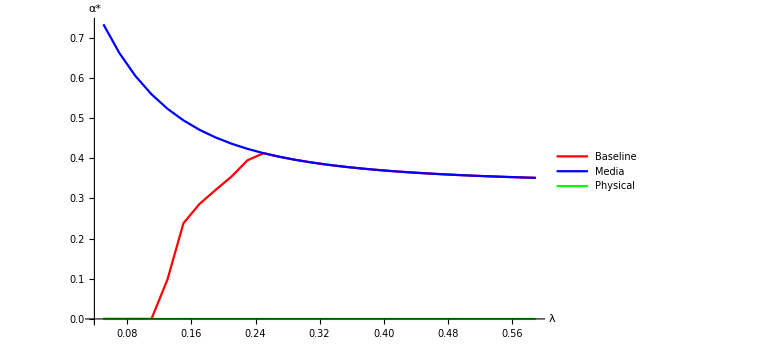

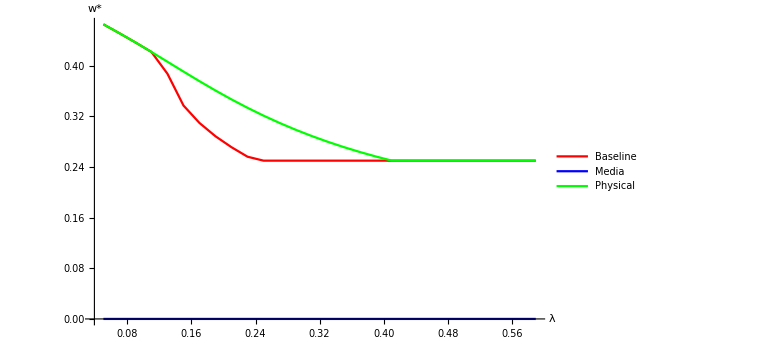

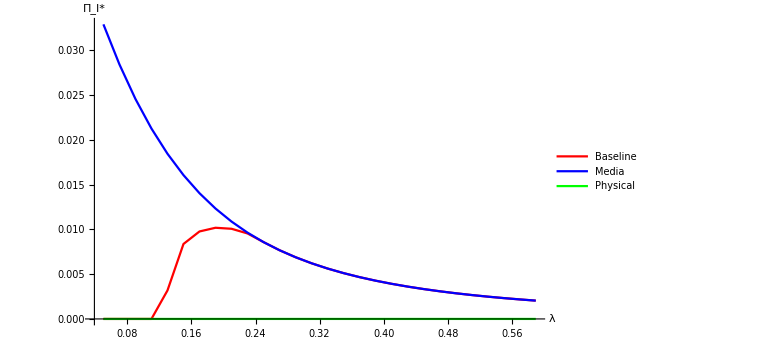

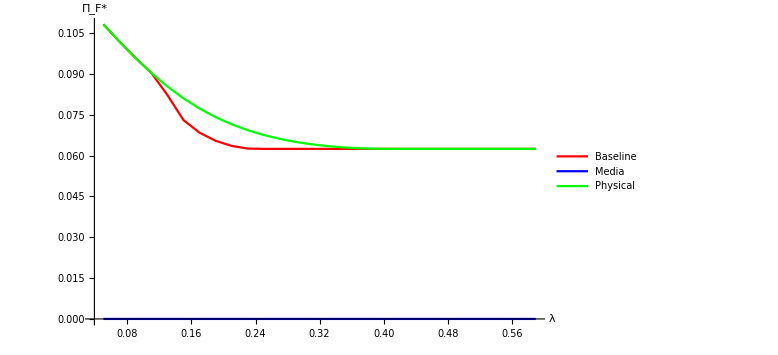

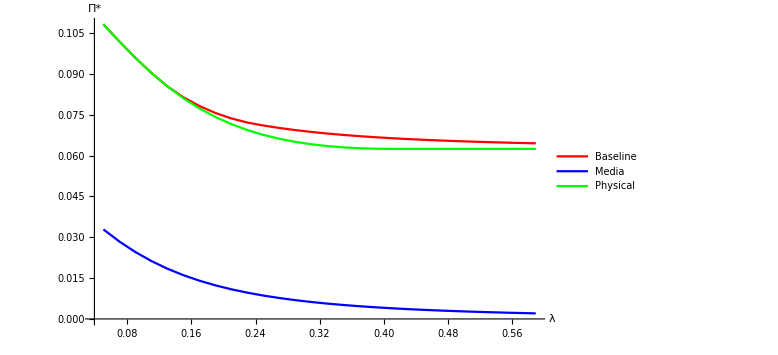

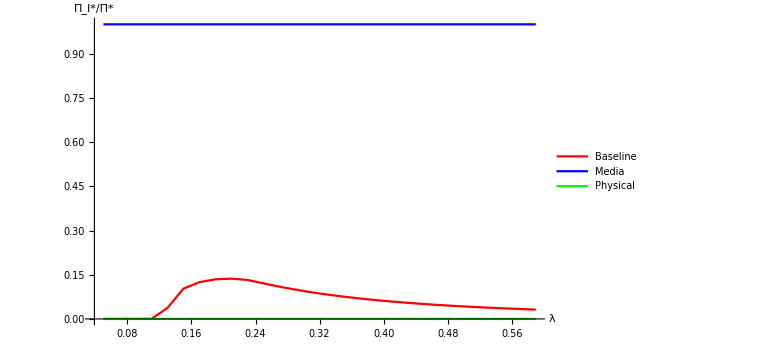

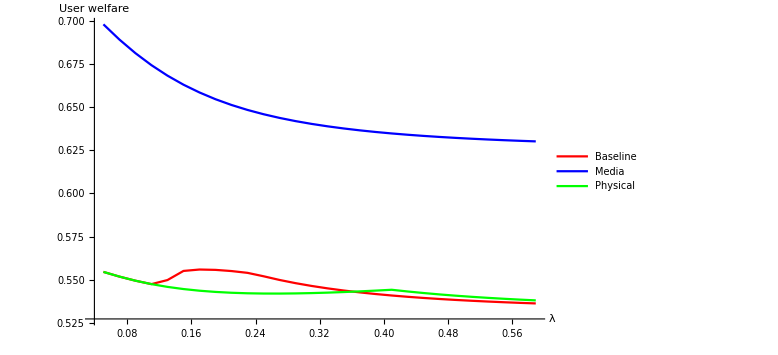

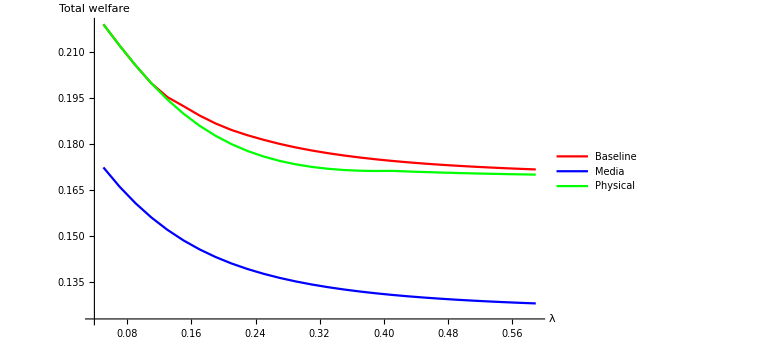

```mathematica
(* =========================================================*)(*0. CLEAN START*)(* =========================================================*)ClearAll["Global`*"];

(* =========================================================*)
(*1. CORE MODEL PRIMITIVES*)
(* =========================================================*)

tau[α_,λ_]:=λ/(1-α);
delta[α_,λ_]:=Exp[-1/tau[α,λ]];

eps0[α_,w_,λ_]:=tau[α,λ] Log[2/(1+Exp[-1/tau[α,λ]])]-w;
eps1[α_,w_,λ_]:=-tau[α,λ] Log[2/(1+Exp[1/tau[α,λ]])]-w;

BfromEps[α_,w_,x_,λ_]:=Exp[(x+w)/tau[α,λ]];

kStar[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{d=delta[α,λ]},-((d+1) B-2)/(2 d B^2-(d+1) B)];

PHint[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{k=kStar[α,B,λ],d=delta[α,λ]},1/(1+k d B)];

PLint[α_?NumericQ,B_?NumericQ,λ_?NumericQ]:=Module[{k=kStar[α,B,λ]},1/(1+k B)];

PHx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{B=BfromEps[α,w,x,λ],x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x<x0,1,x>x1,0,True,PHint[α,B,λ]]];

PLx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{B=BfromEps[α,w,x,λ],x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x<x0,1,x>x1,0,True,PLint[α,B,λ]]];

Px[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=(PHx[α,w,x,λ]+PLx[α,w,x,λ])/2;

KL[p_?NumericQ,q_?NumericQ]:=Which[p==0||p==1,0,q==0||q==1,0,True,p Log[p/q]+(1-p) Log[(1-p)/(1-q)]];

MIx[α_?NumericQ,w_?NumericQ,x_?NumericQ,λ_?NumericQ]:=Module[{ph,pl,p},ph=PHx[α,w,x,λ];
pl=PLx[α,w,x,λ];
p=(ph+pl)/2;
1/2 KL[ph,p]+1/2 KL[pl,p]];

(* =========================================================*)
(*2. USER UTILITY AND WELFARE*)
(* =========================================================*)

Ueq[α_?NumericQ,w_?NumericQ,λ_?NumericQ][x_?NumericQ]:=Module[{x0,x1,ph,pl,mi},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x<x0,0.5-w,x>x1,x,True,ph=PHx[α,w,x,λ];
pl=PLx[α,w,x,λ];
mi=MIx[α,w,x,λ];
0.5 (ph (1-w)+pl (-w)+(2-ph-pl) x)-λ mi]];

UserWelfare[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=NIntegrate[Ueq[α,w,λ][x],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->30,AccuracyGoal->8,PrecisionGoal->8];

(* =========================================================*)
(*3. PLATFORM PROFITS*)
(* =========================================================*)

PiI[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x0>=0,(λ α)/(1-α)*NIntegrate[MIx[α,w,x,λ],{x,x0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}],x0<0<x1,(λ α)/(1-α)*NIntegrate[MIx[α,w,x,λ],{x,0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}],True,0]];

PiF[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=Module[{x0,x1},x0=eps0[α,w,λ];
x1=eps1[α,w,λ];
Which[x0>=0,w*NIntegrate[Px[α,w,x,λ],{x,x0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]+x0*w,x0<0<x1,w*NIntegrate[Px[α,w,x,λ],{x,0,x1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}],True,0]];

PiTotal[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=PiF[α,w,λ]+PiI[α,w,λ];
ku=1/5;
TotalWelfare[α_?NumericQ,w_?NumericQ,λ_?NumericQ]:=PiTotal[α,w,λ]+ku*UserWelfare[α,w,λ];

(* =========================================================*)
(*4. OPTIMIZATION ROUTINES*)
(* =========================================================*)

(*Baseline/joint:choose α and w*)
SolveJoint[λ_?NumericQ]:=Module[{sol,αStar,wStar},sol=NMaximize[{PiTotal[α,w,λ],0<=α<=0.95&&0<=w<=0.5},{α,w},Method->"NelderMead"];
αStar=α/. sol[[2]];
wStar=w/. sol[[2]];
<|"Lambda"->λ,"Alpha"->αStar,"w"->wStar,"PiI"->PiI[αStar,wStar,λ],"PiF"->PiF[αStar,wStar,λ],"Pi"->PiTotal[αStar,wStar,λ],"UserWelfare"->UserWelfare[αStar,wStar,λ],"TotalWelfare"->TotalWelfare[αStar,wStar,λ]|>];

(*Media:choose α only,fix w=0*)
SolveMedia[λ_?NumericQ]:=Module[{sol,αStar,wStar=0.},sol=NMaximize[{PiTotal[α,0.,λ],0<=α<=0.95},α,Method->"NelderMead"];
αStar=α/. sol[[2]];
<|"Lambda"->λ,"Alpha"->αStar,"w"->wStar,"PiI"->PiI[αStar,wStar,λ],"PiF"->PiF[αStar,wStar,λ],"Pi"->PiTotal[αStar,wStar,λ],"UserWelfare"->UserWelfare[αStar,wStar,λ],"TotalWelfare"->TotalWelfare[αStar,wStar,λ]|>];

(*Physical marketplace:choose w only,fix α=0*)
SolvePhysical[λ_?NumericQ]:=Module[{sol,αStar=0.,wStar},sol=NMaximize[{PiTotal[0.,w,λ],0<=w<=0.5},w,Method->"NelderMead"];
wStar=w/. sol[[2]];
<|"Lambda"->λ,"Alpha"->αStar,"w"->wStar,"PiI"->PiI[αStar,wStar,λ],"PiF"->PiF[αStar,wStar,λ],"Pi"->PiTotal[αStar,wStar,λ],"UserWelfare"->UserWelfare[αStar,wStar,λ],"TotalWelfare"->TotalWelfare[αStar,wStar,λ]|>];

(* =========================================================*)
(*5. RUN ON A λ GRID*)
(* =========================================================*)

lambdaGrid=N@Range[0.05,0.6,0.02];

jointResults=SolveJoint/@lambdaGrid;
mediaResults=SolveMedia/@lambdaGrid;
physicalResults=SolvePhysical/@lambdaGrid;

(* =========================================================*)
(*6. EXTRACT INTO A SINGLE ASSOCIATION*)
(* =========================================================*)

toSeries[data_,key_]:=({#["Lambda"],#[key]}&)/@data;

extract=<|"AlphaJoint"->toSeries[jointResults,"Alpha"],"AlphaMedia"->toSeries[mediaResults,"Alpha"],"AlphaPhysical"->toSeries[physicalResults,"Alpha"],"wJoint"->toSeries[jointResults,"w"],"wMedia"->toSeries[mediaResults,"w"],"wPhysical"->toSeries[physicalResults,"w"],"PiIJoint"->toSeries[jointResults,"PiI"],"PiIMedia"->toSeries[mediaResults,"PiI"],"PiIPhysical"->toSeries[physicalResults,"PiI"],"PiFJoint"->toSeries[jointResults,"PiF"],"PiFMedia"->toSeries[mediaResults,"PiF"],"PiFPhysical"->toSeries[physicalResults,"PiF"],"PiJoint"->toSeries[jointResults,"Pi"],"PiMedia"->toSeries[mediaResults,"Pi"],"PiPhysical"->toSeries[physicalResults,"Pi"],"UserWelfareJoint"->toSeries[jointResults,"UserWelfare"],"UserWelfareMedia"->toSeries[mediaResults,"UserWelfare"],"UserWelfarePhysical"->toSeries[physicalResults,"UserWelfare"],"TotalWelfareJoint"->toSeries[jointResults,"TotalWelfare"],"TotalWelfareMedia"->toSeries[mediaResults,"TotalWelfare"],"TotalWelfarePhysical"->toSeries[physicalResults,"TotalWelfare"]|>;

extract["RatioJoint"]=MapThread[{#1[[1]],If[#2[[2]]==0,0,#1[[2]]/#2[[2]]]}&,{extract["PiIJoint"],extract["PiJoint"]}];

extract["RatioMedia"]=MapThread[{#1[[1]],If[#2[[2]]==0,0,#1[[2]]/#2[[2]]]}&,{extract["PiIMedia"],extract["PiMedia"]}];

extract["RatioPhysical"]=MapThread[{#1[[1]],If[#2[[2]]==0,0,#1[[2]]/#2[[2]]]}&,{extract["PiIPhysical"],extract["PiPhysical"]}];

(* =========================================================*)
(*7. PLOTTING UTILITIES*)
(* =========================================================*)

plot3[keyJoint_,keyMedia_,keyPhysical_,ylab_]:=ListLinePlot[{extract[keyJoint],extract[keyMedia],extract[keyPhysical]},PlotLegends->{"Baseline","Media","Physical"},AxesLabel->{"λ",ylab},PlotRange->All,PlotStyle->{Red,Blue,Green},ImageSize->Large];

plot1[key_,ylab_]:=ListLinePlot[{extract[key]},PlotLegends->{"Baseline"},AxesLabel->{"λ",ylab},PlotRange->All,PlotStyle->{Red},ImageSize->Large];

(* =========================================================*)
(*8. STANDARD PLOTS*)
(* =========================================================*)

plot3["AlphaJoint","AlphaMedia","AlphaPhysical","α*"]
plot3["wJoint","wMedia","wPhysical","w*"]
plot3["PiIJoint","PiIMedia","PiIPhysical","Π_I*"]
plot3["PiFJoint","PiFMedia","PiFPhysical","Π_F*"]
plot3["PiJoint","PiMedia","PiPhysical","Π*"]
plot3["RatioJoint","RatioMedia","RatioPhysical","Π_I*/Π*"]

(*New welfare plots*)
plot3["UserWelfareJoint","UserWelfareMedia","UserWelfarePhysical","User welfare"]
plot3["TotalWelfareJoint","TotalWelfareMedia","TotalWelfarePhysical","Total welfare"]

(* =========================================================*)(*9. ADDITIONAL PLOTTING UTILITIES*)(* =========================================================*)(*Same style as plot3,but only baseline/joint*)plotBaseline[key_,ylab_]:=ListLinePlot[{extract[key]},PlotLegends->{"Baseline"},AxesLabel->{"λ",ylab},PlotRange->All,PlotStyle->{Red},ImageSize->Large];

(*Slightly nicer aliases if you prefer*)
plotBaselineAlpha:=plotBaseline["AlphaJoint","α*"];
plotBaselinew:=plotBaseline["wJoint","w*"];
plotBaselinePiI:=plotBaseline["PiIJoint","Π_I*"];
plotBaselinePiF:=plotBaseline["PiFJoint","Π_F*"];
plotBaselinePi:=plotBaseline["PiJoint","Π*"];
plotBaselineRatio:=plotBaseline["RatioJoint","Π_I*/Π*"];
plotBaselineUW:=plotBaseline["UserWelfareJoint","User welfare"];
plotBaselineTW:=plotBaseline["TotalWelfareJoint","Total welfare"];

(* =========================================================*)
(*10. SINGLE-λ SOLVERS FOR UTILITY COMPARISON PLOTS*)
(* =========================================================*)

(*These mirror your original code but use the organized functions*)

SolveAtLambdaAll[λ_?NumericQ]:=Module[{joint,media,physical},joint=SolveJoint[λ];
media=SolveMedia[λ];
physical=SolvePhysical[λ];
<|"Lambda"->λ,"AlphaJoint"->joint["Alpha"],"wJoint"->joint["w"],"PiJoint"->joint["Pi"],"PiIJoint"->joint["PiI"],"PiFJoint"->joint["PiF"],"AlphaMedia"->media["Alpha"],"wMedia"->media["w"],"PiMedia"->media["Pi"],"PiIMedia"->media["PiI"],"PiFMedia"->media["PiF"],"AlphaPhysical"->physical["Alpha"],"wPhysical"->physical["w"],"PiPhysical"->physical["Pi"],"PiIPhysical"->physical["PiI"],"PiFPhysical"->physical["PiF"]|>];

(*Benchmarks*)
NoMarket[x_]:=x;
NoAdsNoFee[x_]:=(1+x)/2;

(*Plot utility comparison at one λ:baseline eq.,media eq.,physical eq.,no market,no ads/no fee*)
PlotUtilityComparison[λ_?NumericQ]:=Module[{sol,αj,wj,αm,wm,αp,wp},sol=SolveAtLambdaAll[λ];
αj=sol["AlphaJoint"];wj=sol["wJoint"];
αm=sol["AlphaMedia"];wm=sol["wMedia"];
αp=sol["AlphaPhysical"];wp=sol["wPhysical"];
Plot[{Ueq[αj,wj,λ][x],Ueq[αm,wm,λ][x],Ueq[αp,wp,λ][x],NoMarket[x],NoAdsNoFee[x]},{x,0,1},PlotRange->{0,1},PlotStyle->{Red,Blue,Green,{Black,Dashed,Opacity[0.6]},{Black,Dotted,Opacity[0.6]}},AxesLabel->{"ε","E[U[ε]]*"},PlotLegends->{"baseline eq.","media eq.","physical eq.","no market","no ads, no fee"},ImageSize->Large]];

(* =========================================================*)
(*11. BASELINE UTILITY FOR SEVERAL λ VALUES*)
(* =========================================================*)

(*Plot baseline equilibrium utility across several λ values.By default it uses the equilibrium α*(λ),w*(λ) from jointResults.*)

PlotUtilityByLambda[lambdaList_List]:=Module[{assocAlpha,assocW},assocAlpha=Association[extract["AlphaJoint"]];
assocW=Association[extract["wJoint"]];
Plot[Evaluate@Join[Table[Ueq[assocAlpha[λ],assocW[λ],λ][x],{λ,lambdaList}],{NoMarket[x],NoAdsNoFee[x]}],{x,0,1},PlotRange->{0,1},AxesLabel->{"ε","E[U[ε]]*"},PlotLegends->Join[Table[Row[{"baseline eq., λ = ",NumberForm[λ,{3,2}]}],{λ,lambdaList}],{"no market","no ads, no fee"}],PlotStyle->Join[Table[{ColorData["SunsetColors"][1-i/Length[lambdaList]],Thick},{i,Length[lambdaList]}],{{Black,Dashed,Opacity[0.6]},{Black,Dotted,Opacity[0.6]}}],ImageSize->Large]];

(*If you instead want to use fixed α0,w0 across λ values,as in your earlier exploratory plot*)
PlotUtilityByLambdaFixed[lambdaList_List,α0_?NumericQ,w0_?NumericQ]:=Plot[Evaluate@Join[Table[Ueq[α0,w0,λ][x],{λ,lambdaList}],{NoMarket[x],NoAdsNoFee[x]}],{x,0,1},PlotRange->{0,1},AxesLabel->{"ε","E[U[ε]]*"},PlotLegends->Join[Table[Row[{"λ = ",NumberForm[λ,{3,2}]}],{λ,lambdaList}],{"no market","no ads, no fee"}],PlotStyle->Join[Table[{ColorData["SunsetColors"][1-i/Length[lambdaList]],Thick},{i,Length[lambdaList]}],{{Black,Dashed,Opacity[0.6]},{Black,Dotted,Opacity[0.6]}}],ImageSize->Large];

(* =========================================================*)
(*12. EXAMPLES*)
(* =========================================================*)

(*Baseline-only line plots*)
plotBaselineAlpha
plotBaselinew
plotBaselinePiI
plotBaselinePiF
plotBaselinePi
plotBaselineRatio
plotBaselineUW
plotBaselineTW

(*Utility comparison at one λ*)
PlotUtilityComparison[0.2]


(*Fixed (α0,w0) utility curves across λ,if you want the old exploratory version*)
PlotUtilityByLambdaFixed[{0.1,0.2,0.3,0.5,0.8},0.4,0.32]
```

```mathematica
(* =========================================*)(*DIAGNOSTIC BLOCK FOR THE KINK*)(* =========================================*)alphaData=extract["AlphaJoint"];
wData=extract["wJoint"];
piData=extract["PiJoint"];
uwData=extract["UserWelfareJoint"];

(*Build row-by-row diagnostics so there are no association key issues*)
diagData=Table[<|"Lambda"->alphaData[[i,1]],"Alpha"->alphaData[[i,2]],"w"->wData[[i,2]],"Pi"->piData[[i,2]],"UserWelfare"->uwData[[i,2]],"eps0"->eps0[alphaData[[i,2]],wData[[i,2]],alphaData[[i,1]]],"eps1"->eps1[alphaData[[i,2]],wData[[i,2]],alphaData[[i,1]]]|>,{i,Length[alphaData]}];

(*Convert any key into {lambda,value} series*)
diagSeries[key_]:=({#["Lambda"],#[key]}&)/@diagData;

(*----------1) eps0 alone----------*)
eps0Plot=ListLinePlot[{diagSeries["eps0"]},AxesLabel->{"λ","ε0"},PlotStyle->{Red},PlotRange->All,PlotLegends->{"ε0"},ImageSize->Large];

(*----------2) eps1 alone----------*)
eps1Plot=ListLinePlot[{diagSeries["eps1"]},AxesLabel->{"λ","ε1"},PlotStyle->{Blue},PlotRange->All,PlotLegends->{"ε1"},ImageSize->Large];

(*----------3) α*and w*on one figure----------*)
policyPlot=ListLinePlot[{diagSeries["Alpha"],diagSeries["w"]},AxesLabel->{"λ","policy"},PlotStyle->{Red,Blue},PlotRange->All,PlotLegends->{"α*","w*"},ImageSize->Large];

(*----------4) user welfare and profit on one figure----------*)
welfareProfitPlot=ListLinePlot[{diagSeries["UserWelfare"],diagSeries["Pi"]},AxesLabel->{"λ","value"},PlotStyle->{Red,Blue},PlotRange->All,PlotLegends->{"User welfare","Π*"},ImageSize->Large];

(*----------5) Combined diagnostic panel----------*)
GraphicsGrid[{{eps0Plot,eps1Plot},{policyPlot,welfareProfitPlot}},Spacings->{0.8,0.8}]
```

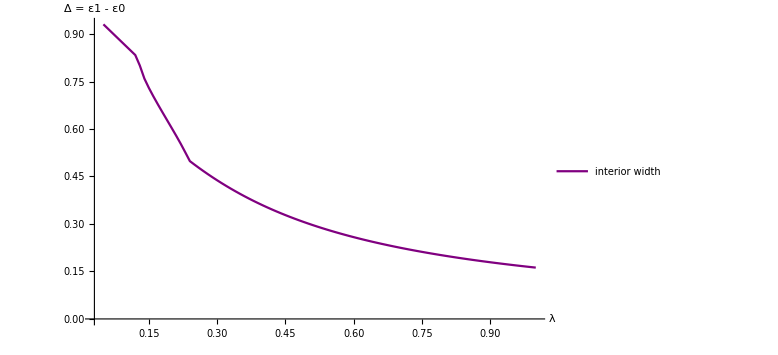

```mathematica
deltaRegionData=Table[{diagData[[i,"Lambda"]],diagData[[i,"eps1"]]-diagData[[i,"eps0"]]},{i,Length[diagData]}];

ListLinePlot[{deltaRegionData},AxesLabel->{"λ","Δ = ε1 - ε0"},PlotStyle->{Purple},PlotRange->All,PlotLegends->{"interior width"},ImageSize->Large]
```

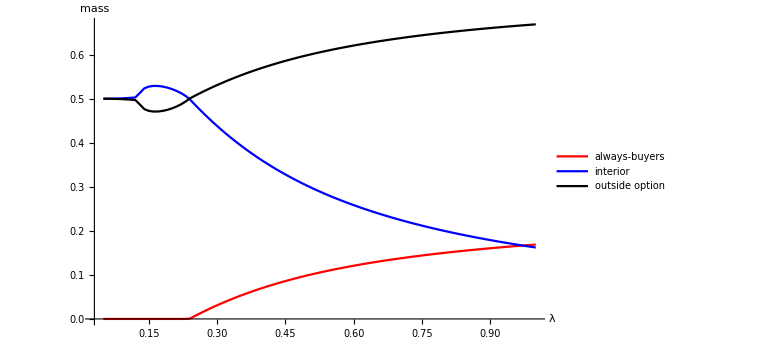

```mathematica
regionMassData=Table[Module[{l=diagData[[i,"Lambda"]],e0=diagData[[i,"eps0"]],e1=diagData[[i,"eps1"]],always,interior,outside},always=Max[0,Min[e0,1]];
interior=Max[0,Min[e1,1]-Max[0,e0]];
outside=1-Max[0,Min[e1,1]];
{l,always,interior,outside}],{i,Length[diagData]}];

ListLinePlot[{regionMassData[[All,{1,2}]],regionMassData[[All,{1,3}]],regionMassData[[All,{1,4}]]},AxesLabel->{"λ","mass"},PlotStyle->{Red,Blue,Black},PlotLegends->{"always-buyers","interior","outside option"},PlotRange->All,ImageSize->Large]
```